```mathematica
BeginPackage["OrigamiReference2D`"]; 

(* vector utilities *)
rotate[{x_,y_},θ_]:={Cos[θ]x-Sin[θ]y,Sin[θ]x+Cos[θ]y};
rotate90[v_]:=rotate[v,π/2];
norm[{x_,y_}]:=Sqrt[x*x+y*y];
normalize[v_]:=v/norm[v];

(* line utilities *)
parallel[{p1_,p2_},{p3_,p4_}]:=(p2-p1).rotate90[p4-p3]==0;
perpendicular[{p1_,p2_},{p3_,p4_}]:=(p2-p1).(p4-p3)==0;
linesEqual[{p1_,p2_},{p3_,p4_}]:=parallel[{p1,p2},{p3,p4}]&&liesOnLine[p1,{p3,p4}];

projectVector[v1_,v2_]:=(v1.v2/v2.v2 )v2;
projectOnLine[p_,{p1_,p2_}]:=p1+projectVector[p-p1,p2-p1];
reflectAcross[p_,l_]:=2 projectOnLine[p,l]-p;
liesOnLine[p_,l_]:=p==projectOnLine[p,l];
liesOnLineSegment[p_,{p1_,p2_}]:=liesOnLine[p,{p1,p2}]&&0≤(p-p1).(p2-p1)/((p2-p1).(p2-p1))≤1;
pointLineDist[p_,l_]:=norm[p-projectOnLine[p,l]];
(* line and line segment intersectinos *)
(* from https://en.wikipedia.org/wiki/Line%E2%80%93line_intersection *)
lineIntersection[{{x1_,y1_},{x2_,y2_}},{{x3_,y3_},{x4_,y4_}}]:=
{
((x1 y2-y1 x2)(x3-x4)-(x1-x2)(x3 y4-y3 x4))/((x1-x2)(y3-y4)-(y1-y2)(x3-x4)),
((x1 y2-y1 x2)(y3-y4)-(y1-y2)(x3 y4-y3 x4))/((x1-x2)(y3-y4)-(y1-y2)(x3-x4))
};

(* the seven origami axioms *)
axiom1[p1_,p2_]:={{p1,p2}};
axiom2[p1_,p2_]:={{(p1+p2)/2,rotate90[p2-p1]+(p1+p2)/2}};
axiom3[{p1_,p2_},{p3_,p4_}]:=
Module[{p,u,v},
If[parallel[{p1,p2},{p3,p4}],
{{(p1+p3)/2,(p1+p4)/2}},
p=lineIntersection[{p1,p2},{p3,p4}];
u=normalize[p2-p1];
v=normalize[p4-p3];
{{p,p+u+v},{p,p+u-v}}
]
];
axiom4[p_,{p1_,p2_}]:={{p,p+rotate90[p2-p1]}};
axiom5[p1_,p2_,{p3_,p4_}]:=
Module[{a,b,c,disc,t1,t2},
a=(p4-p3).(p4-p3);
b=-2(p2-p3).(p4-p3);
c=p3.p3-p1.p1+2p1.p2-2p3.p2;
disc=b^2-4a c;
Which[
disc>0,
t1=(-b+Sqrt[disc])/(2a);
t2=(-b-Sqrt[disc])/(2a);
Join[axiom2[p1,p3+t1(p4-p3)],axiom2[p1,p3+t2(p4-p3)]],
disc==0,
t1=-b/(2a);
axiom2[p1,p3+t1(p4-p3)],
disc<0,
{}
]
];


plotPoint[p_,range_:5,axes_:False]:=Graphics[{PointSize[0.02],Point[p]},PlotRange->range*{{-1,1},{-1,1}},Axes->axes];
plotLine[{p1_,p2_},range_:5,axes_:False]:=ParametricPlot[p1+t(p2-p1),{t,-100,100},PlotRange->range*{{-1,1},{-1,1}},Axes->axes];
plotLineSegment[{p1_,p2_},range_:5,axes_:False]:=ParametricPlot[p1+t(p2-p1),{t,0,1},PlotRange->range*{{-1,1},{-1,1}},Axes->axes];

plotGraphics[points_,lines_,linesegs_,range_:5,axes_:False]:=Show[
plotLine[#,range,axes]&/@lines,
plotLineSegment[#,range,axes]&/@linesegs,
plotPoint[#,range,axes]&/@points
];

EndPackage[];
```

lineSegmentIntersection

```mathematica
boundarypoints={{0,0},{1,0},{1,1},{1,0}};
origami={
(* boundary *)
{{0,0},{1,0},{1,1},{0,1}},
(* points *)
{{0,0},{1,0},{1,1},{0,1}},
(* lines *)
Subsets[{{0,0},{1,0},{1,1},{0,1}},{2}]
};
```

```mathematica
Flatten[(axiom1[#1,#2]&@@@Subsets[{{0,0},{1,0},{1,1},{0,1}},{2}]),1]
```

{{{0,0},{1,0}},{{0,0},{1,1}},{{0,0},{0,1}},{{1,0},{1,1}},{{1,0},{0,1}},{{1,1},{0,1}}}

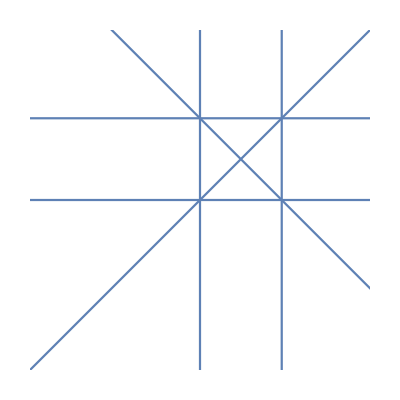

```mathematica
plotGraphics[{},DeleteDuplicates[%,linesEqual],{},2]
```

```mathematica
Partition[Range[6],2,1,1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,1}}